# AntonAntonov/RakuppLink

Functions for interacting with Rakupp (Raku++)

## Paclet Manifest

"Documentation"

"English"

"Guides"

"RakuppInterfaceFunctions.nb"DocumentationEnglishGuidesRakuppInterfaceFunctions.nb

"ReferencePages"

"Symbols"

"RakuppCall.nb"DocumentationEnglishReferencePagesSymbolsRakuppCall.nb

"RakuppCan.nb"DocumentationEnglishReferencePagesSymbolsRakuppCan.nb

"RakuppClose.nb"DocumentationEnglishReferencePagesSymbolsRakuppClose.nb

"RakuppElems.nb"DocumentationEnglishReferencePagesSymbolsRakuppElems.nb

"RakuppEval.nb"DocumentationEnglishReferencePagesSymbolsRakuppEval.nb

"RakuppGrammarFromFile.nb"DocumentationEnglishReferencePagesSymbolsRakuppGrammarFromFile.nb

"RakuppGrammarFromSource.nb"DocumentationEnglishReferencePagesSymbolsRakuppGrammarFromSource.nb

"RakuppGrammar.nb"DocumentationEnglishReferencePagesSymbolsRakuppGrammar.nb

"RakuppInt.nb"DocumentationEnglishReferencePagesSymbolsRakuppInt.nb

"RakuppLoad.nb"DocumentationEnglishReferencePagesSymbolsRakuppLoad.nb

"RakuppMade.nb"DocumentationEnglishReferencePagesSymbolsRakuppMade.nb

"RakuppMatchedQ.nb"DocumentationEnglishReferencePagesSymbolsRakuppMatchedQ.nb

"RakuppMatch.nb"DocumentationEnglishReferencePagesSymbolsRakuppMatch.nb

"RakuppNum.nb"DocumentationEnglishReferencePagesSymbolsRakuppNum.nb

"RakuppParse.nb"DocumentationEnglishReferencePagesSymbolsRakuppParse.nb

"RakuppShutdown.nb"DocumentationEnglishReferencePagesSymbolsRakuppShutdown.nb

"RakuppStr.nb"DocumentationEnglishReferencePagesSymbolsRakuppStr.nb

"RakuppTree.nb"DocumentationEnglishReferencePagesSymbolsRakuppTree.nb

"RakuppVersion.nb"DocumentationEnglishReferencePagesSymbolsRakuppVersion.nb

"Tutorials"

"Kernel"

"RakuppLink.wl"KernelRakuppLink.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

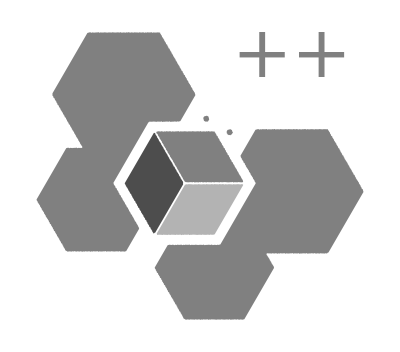

### Basic Description

Rakupp interpreter interaction functions based on Foreign Function Interface.

### Details

Rakupp is a from-scratch implementation of the Raku programming language in C++17.

The Wolfram Language (WL) binding is one of the bindings provided by Rakupp's GitHub repository.

Rakupp has to be installed before using this paclet -- see the direections in Rakupp's main README and WL's binding README.

One interpreter per Wolfram kernel process, created on first use.

One kernel thread talks to it (Raku code inside threads freely).

### Primary Context

AntonAntonov`RakuppLink`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`RakuppLink`"];
```

### Basic Examples

Setup the RAKUPP_LIB environmental variable:

```mathematica
SetEnvironment["RAKUPP_LIB"->FileNameJoin[{$HomeDirectory,".local","lib","librakupp.dylib"}]]
```

Evaluate a simple arithmetic expression with Rakupp:

```mathematica
RakuppEval["2_000 + 232"]
```

2232

Evaluate a^b mod m:

```mathematica
RakuppEval["expmod(3,4,5)"]
```

1

Compare with Wolfram Language PowerMod:

```mathematica
PowerMod[3,4,5]
```

1

### Scope

Rakupp's version:

```mathematica
RakuppVersion[]
```

3.7.0

Evaluate a Raku style pipeline:

```mathematica
RakuppEval["
(1..5) ==> map { $_ * 2 } ==> grep { $_ > 5 }
"]
```

{6,8,10}

Here is a string with a Raku-language defined grammar:

```mathematica
rkCode="
grammar Parser {
    rule  TOP  { <who> <verb> <lang> }
    token who  {:i I | you | we | they }
    token verb { <love> | <hate> }
    token love { '❤️' | '♥' | love }
	token hate { '🤮' | hate }
    token lang {:i < Raku Rust Go Python Ruby TypeScript PHP WL> }
}
";
```

Compile the grammar in Rakupp interpreter:

```mathematica
g=RakuppGrammarFromSource[rkCode]
```

RakuppGrammar[0,<anonymous>]

Parse a sentence:

```mathematica
m=RakuppParse[g,"We 🤮 python"]
```

RakuppMatch[OpaqueRawPointer[…]]

Show the tree corresponding to the obtained match object:

```mathematica
RakuppTree[m]
```

<|lang→python,verb→<|hate→🤮|>,who→We|>

Free the interpreter:

```mathematica
RakuppShutdown[]
```

Define a Raku sub:

```mathematica
RakuppEval["
proto sub fib (Int $n --> Int) {*}
multi sub fib (0)  { 0 }
multi sub fib (1)  { 1 }
multi sub fib ($n) { fib($n - 1) + fib($n - 2) }
"]
```

&fib

Evaluate using RakuppCall:

```mathematica
RakuppCall["fib",12]
```

144

```mathematica
Fibonacci[12]
```

144

Notebook-wide Rakupp evaluations can be done via Rakupp cells in RakuMode notebooks:

-Graphics-

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-RakuppLink-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Raku

rakulang

Perl 6

Rakupp

raku++

c++

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

AntonAntonov/RakuMode

### Original Source References and Attributions

What is Raku++ – Andrew Shitov

### Links

GitHub - ash/rakupp: Raku++ — a Raku language interpreter and compiler written from scratch in C++17

raku.online — Raku playground in the browser

### Compatibility

#### Wolfram Language Version

13.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.